```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.5,
RandomReal[], (* Prob to buy tool *)
RandomReal[], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&nPTools<=maxPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3,4]
```

{{0,0,1,5,-10},7}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]],a4=agent[[4]],a5=agent[[5]]},
{p,MutateValue[pb],MutateValue[pd],a4,a5}
];
```

0.275068

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=poolHealth/fullToolHealth;
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,800,200];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/4];
newAgents=Join[newAgents,newAgents,newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.1,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,800,200];
history=Append[history, ph];
{ag, history}
];
```

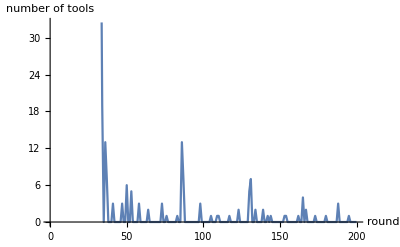

170.86

{{0.5,0,0.0725338,0,300},{0.5,0,0.0725338,0,264},{0.5,0,0.0725338,0,264},{0.5,0,0.0725338,0,261},{0.5,0.0112749,0.0745417,0,253},{0.5,0,0.0725338,0,249},{0.5,0,0.0725338,0,248},{0.5,0,0.0725338,0,245},{0.5,0,0.0725338,0,244},{0.5,0,0.0725338,0,240},{0.5,0,0.0725338,0,240},{0.5,0,0.0725338,0,232},{0.5,0,0.0725338,0,231},{0.5,0,0.0725338,0,227},{0.5,0,0.0725338,0,226},{0.5,0,0.0725338,0,226},{0.5,0,0.0725338,0,223},{0.5,0,0.0725338,0,223},{0.5,0,0.0725338,0,221},{0.5,0,0.0725338,0,220},{0.5,0,0.0725338,0,219},{0.5,0,0.0725338,0,216},{0.5,0,0.0725338,0,215},{0.5,0,0.0725338,0,210},{0.5,0,0,0,209},{0.5,0,0.0725338,0,208},{0.5,0,0.0725338,0,207},{0.5,0,0.0725338,0,207},{0.5,0,0.0725338,0,206},{0.5,0,0.0725338,0,204},{0.5,0,0.0725338,0,203},{0.5,0,0.0725338,0,203},{0.5,0,0.0725338,0,201},{0.5,0,0.0547388,0,200},{0.5,0,0.0725338,0,200},{0.5,0,0.0725338,0,200},{0.5,0,0.0547388,0,198},{0.5,0,0.0725338,0,196},{0.5,0,0.0725338,0,195},{0.5,0,0,0,194},{0.5,0,0.0725338,0,193},{0.5,0,0.0725338,0,193},{0.5,0,0.0725338,0,192},{0.5,0,0,0,190},{0.5,0,0.0547388,0,189},{0.5,0,0.0725338,0,188},{0.5,0,0.0725338,0,187},{0.5,0,0.0725338,0,185},{0.5,0,0.0725338,0,183},{0.5,0,0.0725338,0,181},{0.5,0,0.0725338,0,179},{0.5,0,0.0725338,0,173},{0.5,0,0.0725338,0,173},{0.5,0,0,0,172},{0.5,0,0.0725338,0,172},{0.5,0,0,0,171},{0.5,0,0,0,169},{0.5,0,0.0725338,0,168},{0.5,0,0.0371924,0,167},{0.5,0,0.0547388,0,167},{0.5,0,0.0547388,0,164},{0.5,0,0.0725338,0,161},{0.5,0,0.0725338,0,158},{0.5,0,0.0725338,0,158},{0.5,0,0,0,156},{0.5,0,0.0547388,0,156},{0.5,0,0,0,155},{0.5,0,0.0725338,0,152},{0.5,0,0.0725338,0,150},{0.5,0,0.0725338,0,147},{0.5,0,0,0,146},{0.5,0,0.0725338,0,146},{0.5,0,0.0725338,0,144},{0.5,0,0.0725338,0,141},{0.5,0,0.0725338,0,138},{0.5,0,0,0,137},{0.5,0,0.0547388,0,136},{0.5,0,0.0725338,0,133},{0.5,0,0.0725338,0,132},{0.5,0,0.0725338,0,132},{0.5,0,0,0,129},{0.5,0,0.0725338,0,129},{0.5,0,0.145187,0,129},{0.5,0,0.0725338,0,128},{0.5,0,0.0725338,0,124},{0.5,0,0.0725338,0,121},{0.5,0,0.0725338,0,119},{0.5,0,0.0725338,0,117},{0.5,0.0531888,0.042796,3,116},{0.5,0,0,0,115},{0.5,0,0.0725338,0,110},{0.5,0,0.0725338,0,109},{0.5,0,0.0725338,0,107},{0.5,0,0,0,104},{0.5,0,0.0593494,0,77},{0.5,0,0.178996,0,62},{0.5,0.0574112,0.13247,0,38},{0.5,0.0240393,0.21723,0,22},{0.5,0,0.25629,0,-105},{0.5,0.0924436,0.330234,3,-127}}

```mathematica
{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]],AxesLabel->{"round", "number of tools"}]
N[Total[Map[Function[x,Last[x]],a]]/Length[a]] (*average payoff*)
Sort[a,Last[#1]>Last[#2]&]
```

We see that we get a mixed stable equilibrium where everyone doesn’t donate that much. Below we plot the evolution of pool health over the generations.

```mathematica
hh={};
For[i=1,i≤Length[h],i++,
For[j=1,j≤Length[h[[i]]],j++,
hh=Append[hh,{i,j,h[[i]][[j]]}];
]
];
ListPlot3D[hh]
```

-Graphics3D-

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},poolHealth=initHealth},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
history=Join[history, ph];
{ag, history}
];
```

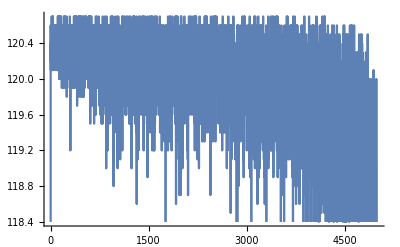

{{0.5,0,0,0,275},{0.5,0,0.0608441,0,270},{0.5,0,0.235488,0,270},{0.5,0,0.0300676,0,255},{0.5,0,0.1085,0,255},{0.5,0,0.1085,0,250},{0.5,0,0.0608441,0,245},{0.5,0,0.10212,0,240},{0.5,0,0.1085,0,240},{0.5,0,0.1085,0,240},{0.5,0,0.0931126,0,235},{0.5,0.00311599,0.137696,0,230},{0.5,0,0,0,225},{0.5,0.0443687,0.0358325,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.1085,0,225},{0.5,0,0.235488,0,225},{0.5,0,0.1085,0,220},{0.5,0,0.1085,0,215},{0.5,0,0.1085,0,215},{0.5,0,0.1085,0,215},{0.5,0,0.1085,0,215},{0.5,0,0.235488,0,215},{0.5,0,0.0608441,0,210},{0.5,0,0.1085,0,210},{0.5,0,0.1085,0,210},{0.5,0.00311599,0.137696,0,210},{0.5,0,0.0931126,0,205},{0.5,0,0.1085,0,205},{0.5,0,0.1085,0,205},{0.5,0,0.1085,0,205},{0.5,0,0.1085,0,200},{0.5,0,0.1085,0,200},{0.5,0,0.1085,0,200},{0.5,0,0.235488,0,200},{0.5,0,0.10212,0,195},{0.5,0,0.1085,0,195},{0.5,0,0.1085,0,195},{0.5,0,0.1085,0,195},{0.5,0,0.0937535,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.1085,0,190},{0.5,0,0.0931126,0,185},{0.5,0,0.1085,0,185},{0.5,0,0.271267,0,185},{0.5,0,0.1085,0,180},{0.5,0,0.1085,0,180},{0.5,0,0.1085,0,180},{0.5,0,0.1085,0,180},{0.5,0,0.1085,0,180},{0.5,0,0.1085,0,180},{0.5,0,0.0931126,0,175},{0.5,0,0.1085,0,175},{0.5,0,0.1085,0,175},{0.5,0,0.137616,0,175},{0.5,0,0.271267,0,170},{0.5,0,0.1085,0,165},{0.5,0,0.157724,0,165},{0.5,0,0.1085,0,160},{0.5,0,0.209634,0,160},{0.5,0,0.425391,0,160},{0.5,0,0.1085,0,155},{0.5,0,0.1085,0,155},{0.5,0.0147747,0.242938,0,155},{0.5,0,0.1085,0,150},{0.5,0,0.1085,0,150},{0.5,0,0.210768,0,150},{0.5,0,0.1085,0,145},{0.5,0,0.1085,0,145},{0.5,0,0.210768,0,145},{0.5,0,0.229175,0,145},{0.5,0,0.168625,0,140},{0.5,0,0.271267,0,140},{0.5,0,0.271267,0,140},{0.5,0.00311599,0.137696,0,135},{0.5,0.00311599,0.137696,0,130},{0.5,0,0.235488,0,130},{0.5,0,0.271267,0,130},{0.5,0,0.1085,0,125},{0.5,0,0.271267,0,125},{0.5,0,0.1085,0,120},{0.5,0,0.169105,0,120},{0.5,0,0.157724,0,115},{0.5,0,0.235488,0,115},{0.5,0,0.209634,0,100},{0.5,0,0.235488,0,100},{0.5,0,0.271267,0,100},{0.5,0,0.235488,0,95},{0.5,0,0.235488,0,85},{0.5,0.105294,0.168325,2,75},{0.5,0,0.271267,0,70},{0.5,0,0.544523,0,-20}}

```mathematica
{a,h}=RunSimContinuous[agentParams,800];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"}](* plot the number of tools in the pool at any given time *)
Sort[a,Last[#1]>Last[#2]&]
```

In the above example we see a working pool where agents buy tools seldom and borrow more often. We also see that the pool is kept running by a few volunteers, everyone is not donating to the pool.